```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
(*Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/RydbergInstaSWAPGerardCZ.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv"]; (*Imported gates from Qiskit*)*)
Import["C:\\Users\\KitKa\\QuESTlink\\Link\\QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["C:\\Users\\KitKa\\QuESTlink\\quest_link.exe"];(*Creating QuEST environment*)Import["C:\\Users\\KitKa\\QuESTlink\\RydbergGerardCZDCSWAP.wl"];(*Configuration File*)data=Import["C:\\Users\\KitKa\\OneDrive\\Documents\\Wolfram Mathematica\\SU4Gates9Qubits.csv"];
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}],
(* blockade radius in μm*)
BlockadeRadius->Sqrt[2],
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

-Graphics3D-

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[ToExpression@StringSplit[IntegerString[i,2,NQ],""],{i,0,2^NQ-1,1}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure*)

MeasErrors[QubitList_]:=Table[Subscript[U,QubitList[[i]]][{{0.9997,0},{0,1.0003}}],{i,1,Length[QubitList]}]
```

```mathematica
KetList[3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
(*Gate,Initialisation and Measurement Errors*)
SU4Gate[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP], a[[1]],a[[2]]],Subscript[CZ, a[[2]],a[[1]]][Pi]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]

(*SU4Gate[data[[400;;1000]][[112]],0,1]*)

(*Generate a list of random permutations of NQ qubits*)
NRandQbits[NQ_]:=RandomSample[Range[0,NQ-1],NQ]

(*Compute the probability of getting a heavy output of the model circuit from the noisy circuit THIS STILL AIN'T RIGHT*)
CheckHeavyOutputProb[PoutcomesIMPLEMENTED_,PoutcomesMODEL_]:=Pick[PoutcomesIMPLEMENTED,Table[If[PoutcomesMODEL[[i]]>=Median[PoutcomesMODEL],True,False],{i,1,Length[PoutcomesMODEL]}]];

(*Generate a layer of gates for building a QV circuit*)
QVLayer[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4Gate[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[SWAP, RQs[[n+1]],3]},SU4Gate[DataSet[[n+i]],RQs[[n]],3]],{Subscript[SWAP, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];
(*Generate initialisation layer of circuit*)
InitCirc[Reg_,MaxNQ_]:=Table[Subscript[Init, b],{b,0,MaxNQ-1,1}]

(*Generate circuit of m=d layers of SU(4) gates*)
QVCirc[DataSet_,NQ_]:=Table[RQS=NRandQbits[NQ];Layer=QVLayer[DataSet,NQ,RQS,i];
(*Print["# Qubits, ",NQ," # Gates per Layer, ",Length[Layer]]*);Flatten[Layer],{i,0,NQ-1,1}]

(*Generating and applying the circuits to a register and getting the probability of a heavy output*)
QVProcedure[DataSet_,NQ_, MaxNQ_,NReps_,Reg_]:=Table[
Circ1=QVCirc[DataSet[[NQ*Quotient[NQ,2]*Rep+1;;NQ*Quotient[NQ,2]*(Rep+1)]],NQ];
Initialisation=InitCirc[Reg,MaxNQ];
InitCircuit=Flatten[Join[Initialisation,Circ1]];
CircNoisy=ExtractCircuit[InsertCircuitNoise[InitCircuit,RydDev,ReplaceAliases->True]];
CircModel=ExtractCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]];
SetQuregMatrix[Reg,RandomMixState[MaxNQ]];
ApplyCircuit[Reg,CircNoisy];
(*ApplyCircuit[Reg,MeasErrors[Reverse[Range[0,NQ-1]]]]*);
     PoutcomesNoisy=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[PoutcomesNoisy];*)
InitZeroState[Reg];
(*Print[DrawCircuit[CircModel]];*)
ApplyCircuit[Reg,CircModel];
PoutcomesModel=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[NQ, " Model Outcomes Probabilities ",PoutcomesModel," Noisy Outcome Probabilities ",PoutcomesNoisy];*)
HeavyOutputs=CheckHeavyOutputProb[PoutcomesNoisy,PoutcomesModel];
Total[HeavyOutputs],{Rep,0,NReps-1,1}]


(*Put everything together and get a value for Quantum Volume*)
QVCalc[DataSet_,MaxNQ_,NReps_]:=Table[ρ=CreateDensityQureg[MaxNQ];
HOP=QVProcedure[DSSplice=DataSet[[(Total[Table[a*Quotient[a,2],{a,0,NQ-1}]]*NReps)+1 ;;Total[Table[a*Quotient[a,2],{a,0,NQ}]*NReps]]],NQ,MaxNQ,NReps,ρ];
MHOP=Mean[HOP];
σ=StandardDeviation[HOP]/Sqrt[NReps-1];;
If[ Re[(MHOP-2σ)]>2/3,VQ=2^NQ,VQ=0];
Print[{"Layer",NQ,VQ}];
{NQ,MHOP±2σ}
,{NQ,2,MaxNQ,1}];



SWAPQV=AbsoluteTiming[QVCalc[data,9,200]];
Print[SWAPQV[[2]]]
DestroyAllQuregs[];
```

{Layer,2,4}

{Layer,3,8}

{Layer,4,16}

{Layer,5,32}

{Layer,6,64}

{Layer,7,0}

{Layer,8,0}

{Layer,9,0}

{{2,0.736428±0.0131019},{3,0.786161±0.0120597},{4,0.757936±0.00674214},{5,0.743349±0.00516281},{6,0.689238±0.00351049},{7,0.662192±0.00303179},{8,0.590931±0.00269218},{9,0.558019±0.00236677}}

```mathematica
?UNonNorm
```

```mathematica
?QuEST`Gate`*
```

Missing[UnknownSymbol,QuEST`Gate`UNonNorm]

```mathematica
RydDev[Gates]
```

{Init_q$_Integer:>Association[UpdateVariables→((lossAtom$17118[q$]=False;lossAtomProb$17118[q$]=0;)&),NoisyForm→{Damp_q$[1],KrausNonTP_q$[{{{√(1-userconfig[LeakProbInit]),0},{0,1}}}]},GateDuration→userconfig[DurInit]],Wait_qubits$__[dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={}:>Association[NoisyForm→Table[passiveNoise$17118[q,dur$],{q,Flatten[{qubits$}]}],GateDuration→dur$],M_q$_Integer:>Association[UpdateVariables→((lossAtomProb$17118[q$]+=userconfig[AtomLossMeas]/100;)&),NoisyForm→{Depol_q$[percent2infidel[userconfig[FidMeas]]],M_q$},GateDuration→userconfig[DurMeas]],SRot_q$_Integer[ϕ$_,Δ$_,tg$_]:>Association[NoisyForm→{SRot_q$[ϕ$,Δ$,tg$],Deph_q$[dephα$17118[tg$]]},GateDuration→tg$],H_q$_Integer:>Association[NoisyForm→{H_q$,Deph_q$[dephα$17118[π/userconfig[Ω]]]},GateDuration→π/userconfig[Ω]],Rx_q$_Integer[θ$_]:>Association[NoisyForm→{Rx_q$[θ$],Deph_q$[dephα$17118[Abs[θ$/π]/userconfig[Ω]]]},GateDuration→Abs[θ$]/userconfig[Ω]],Ry_q$_Integer[θ$_]:>Association[NoisyForm→{Ry_q$[θ$],Deph_q$[dephα$17118[Abs[θ$/π]/userconfig[Ω]]]},GateDuration→Abs[θ$]/userconfig[Ω]],Rz_q$_Integer[θ$_]:>Association[NoisyForm→{Rz_q$[θ$],Deph_q$[dephα$17118[Abs[θ$/π]/userconfig[Ω]]]},GateDuration→Abs[θ$]/userconfig[Ω]],SWAP_(q1$_Integer,q2$_Integer):>Association[NoisyForm→{H_q1$,Deph_q1$[dephα$17118[π/userconfig[Ω]]],KrausNonTP_(q1$,q2$)[{{{1,0,0,0},{0,0.999 Exp[ⅈ 0.9906 π],0,0},{0,0,0.999 Exp[ⅈ 0.9906 π],0},{0,0,0,0.9986 Exp[ⅈ π]}}}],H_q1$,Deph_q1$[dephα$17118[π/userconfig[Ω]]],H_q2$,Deph_q1$[dephα$17118[π/userconfig[Ω]]],KrausNonTP_(q2$,q1$)[{{{1,0,0,0},{0,0.999 Exp[ⅈ 0.9906 π],0,0},{0,0,0.999 Exp[ⅈ 0.9906 π],0},{0,0,0,0.9986 Exp[ⅈ π]}}}],H_q2$,Deph_q2$[dephα$17118[π/userconfig[Ω]]],H_q1$,Deph_q1$[dephα$17118[π/userconfig[Ω]]],KrausNonTP_(q1$,q2$)[{{{1,0,0,0},{0,0.999 Exp[ⅈ 0.9906 π],0,0},{0,0,0.999 Exp[ⅈ 0.9906 π],0},{0,0,0,0.9986 Exp[ⅈ π]}}}],H_q1$,Deph_q1$[dephα$17118[π/userconfig[Ω]]]},GateDuration→3.9+(4 π)/userconfig[Ω]],SWAPLoc_(q1$_Integer,q2$_Integer):>Association[UpdateVariables→(({qubitLocs$17118[q1$],qubitLocs$17118[q2$]}={qubitLocs$17118[q2$],qubitLocs$17118[q1$]})&),NoisyForm→Flatten[{passiveNoise$17118[q1$,(4 π)/userconfig[Ω]],passiveNoise$17118[q2$,(4 π)/userconfig[Ω]]}],GateDuration→(4 π)/userconfig[Ω]],ShiftLoc_q$__[v$_]/;LegitShift[Flatten[{q$}],qubitLocs$17118,v$]:>Association[UpdateVariables→((qubitLocs$17118[#1]+=v$&)/@Flatten[{q$}]&),NoisyForm→{},GateDuration→v$⟦1⟧/0.5],CZ_(p$_Integer,q$_Integer)[ϕ$_]/;blockadeCheck$17118[{p$,q$}]:>Association[NoisyForm→{{KrausNonTP_(p$,q$)[{{{1,0,0,0},{0,0.999 Exp[ⅈ 0.9906 π],0,0},{0,0,0.999 Exp[ⅈ 0.9906 π],0},{0,0,0,0.9986 Exp[ⅈ π]}}}]}},GateDuration→1.3],C_c$_[Z_t$__]/;blockadeCheck$17118[{c$,t$}]:>Association[NoisyForm→Join[Table[C_c$[Z_targ],{targ,{t$}}],(KrausNonTP_#1[{{{1,0},{0,√(1-userconfig[LeakProbCZ][11])}}}]&)/@Flatten[{c$,t$}]],GateDuration→(4 π)/userconfig[Ω]],C_c$_[Z_t$__[θ$_]]/;blockadeCheck$17118[{c$,t$}]:>Association[NoisyForm→Join[Table[C_c$[Z_targ],{targ,{t$}}],(KrausNonTP_#1[{{{1,0},{0,√(1-userconfig[LeakProbCZ][11])}}}]&)/@Flatten[{c$,t$}]],GateDuration→(4 π)/userconfig[Ω]],C_c$__[Z_t$_]/;blockadeCheck$17118[{c$,t$}]:>Association[NoisyForm→Join[{C_c$[Z_t$]},(KrausNonTP_#1[{{{1,0},{0,√(1-userconfig[LeakProbCZ][11])}}}]&)/@Flatten[{c$,t$}]],GateDuration→(4 π)/userconfig[Ω]],C_c$__[Z_t$_[θ$_]]:>Association[NoisyForm→Join[{C_c$[Z_t$]},(KrausNonTP_#1[{{{1,0},{0,√(1-userconfig[LeakProbCZ][11])}}}]&)/@Flatten[{c$,t$}]],GateDuration→Abs[θ$]/userconfig[Ω]]}

U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]

-Graphics-

U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]

{X_0,X_1,X_2,H_0,X_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}],X_0,H_0,X_0,X_1,X_2}

{X_0,X_1,X_2,H_0,X_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}],X_0,H_0,X_0,X_1,X_2}

{X_1,X_2,X_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}],X_0,X_1,X_2}

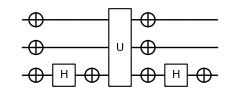

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

-Graphics-

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Toff=Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]
DrawCircuit[{Toff}]
CCZ=Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]
CCZCirc={Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[H, 0],Subscript[X, 0],Toff,Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2]}
ToffCirc={Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[H, 0],Subscript[X, 0],CCZ,Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2]}
CCZClifCirc={Subscript[X,1],Subscript[X,2],Subscript[X, 0],CCZ,Subscript[X, 0],Subscript[X,1],Subscript[X,2]}
DrawCircuit[ToffCirc]
CalcCircuitMatrix[{Toff}]//MatrixForm
CalcCircuitMatrix[ToffCirc]//MatrixForm
DrawCircuit[CCZCirc]
CalcCircuitMatrix[{CCZ}] //MatrixForm
CalcCircuitMatrix[CCZCirc] // MatrixForm
CalcCircuitMatrix[CCZClifCirc]//MatrixForm
```

```mathematica
{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
GroverOracle3Q=Table[SearchSeeds=KetList[3];XIndices=Position[Reverse[SearchSeeds[[i]]],1];Xs=Table[Subscript[X, XIndices[[j]]-1],{j,1,Length[XIndices]}];DrawCircuit[Flatten[{Xs,CCZ,Xs}]],{i,1,2^3}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Subscript[XTrans, i_]:={Subscript[Rx, i][Pi]};
Subscript[HTrans, i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
Subscript[ToffSandBread, t_,c1_,c2_]:={Subscript[Ry, t][-Pi/2],Subscript[Rx, t][-Pi],Subscript[Rx, c1][Pi],Subscript[Rx, c2][Pi]}
```